## 1. Naloga

```mathematica
(1/3 + 1/6)^2
```

1/4

```mathematica
3/(6/8)
```

4

```mathematica
Sin[Pi/2]
```

1

```mathematica
E^Log[7]
```

7

## 2. Naloga

```mathematica
((3 + 4x) / (2 + 5x))^2 + ((2 + x) / (1-x))^2
```

(2+x)^2/(1-x)^2+(3+4 x)^2/(2+5 x)^2

```mathematica
Simplify[(2+x)^2/(1-x)^2+(3+4 x)^2/(2+5 x)^2]
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

```mathematica
Factor[((3 + 4x) / (2 + 5x))^2 + ((2 + x) / (1-x))^2]
```

(25+102 x+161 x^2+112 x^3+41 x^4)/((-1+x)^2 (2+5 x)^2)

```mathematica
Simplify[x/y + y/x + 2]
```

(x+y)^2/(x y)

```mathematica
Simplify[(x^2 + y^2)^2 - 2(xy)^2]
```

-2 xy^2+(x^2+y^2)^2

```mathematica
Simplify[(Sin[x])^2 + (Cos[x])^2]
```

1

```mathematica
Simplify[2Sin[x]Cos[x]]
```

Sin[2 x]

```mathematica
Simplify[(Tan[Pi/8])^4 + (Cot[Pi/8])^4]
```

Cot[π/8]^4+Tan[π/8]^4

```mathematica
FullSimplify[(Tan[Pi/8])^4 + (Cot[Pi/8])^4]
```

34

```mathematica
FullSimplify[Sqrt[278 + 42Sqrt[5] - 12Sqrt[6] - 28Sqrt[30]]]
```

3+7 √5-2 √6

## 3. Naloga

```mathematica
TrigExpand[(x + xy + y)^10]
```

x^10+10 x^9 xy+45 x^8 xy^2+120 x^7 xy^3+210 x^6 xy^4+252 x^5 xy^5+210 x^4 xy^6+120 x^3 xy^7+45 x^2 xy^8+10 x xy^9+xy^10+10 x^9 y+90 x^8 xy y+360 x^7 xy^2 y+840 x^6 xy^3 y+1260 x^5 xy^4 y+1260 x^4 xy^5 y+840 x^3 xy^6 y+360 x^2 xy^7 y+90 x xy^8 y+10 xy^9 y+45 x^8 y^2+360 x^7 xy y^2+1260 x^6 xy^2 y^2+2520 x^5 xy^3 y^2+3150 x^4 xy^4 y^2+2520 x^3 xy^5 y^2+1260 x^2 xy^6 y^2+360 x xy^7 y^2+45 xy^8 y^2+120 x^7 y^3+840 x^6 xy y^3+2520 x^5 xy^2 y^3+4200 x^4 xy^3 y^3+4200 x^3 xy^4 y^3+2520 x^2 xy^5 y^3+840 x xy^6 y^3+120 xy^7 y^3+210 x^6 y^4+1260 x^5 xy y^4+3150 x^4 xy^2 y^4+4200 x^3 xy^3 y^4+3150 x^2 xy^4 y^4+1260 x xy^5 y^4+210 xy^6 y^4+252 x^5 y^5+1260 x^4 xy y^5+2520 x^3 xy^2 y^5+2520 x^2 xy^3 y^5+1260 x xy^4 y^5+252 xy^5 y^5+210 x^4 y^6+840 x^3 xy y^6+1260 x^2 xy^2 y^6+840 x xy^3 y^6+210 xy^4 y^6+120 x^3 y^7+360 x^2 xy y^7+360 x xy^2 y^7+120 xy^3 y^7+45 x^2 y^8+90 x xy y^8+45 xy^2 y^8+10 x y^9+10 xy y^9+y^10

```mathematica
TrigExpand[Sin[x +y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

## 4. Naloga

```mathematica
a = 3;
b = 4;
c = 6;
o = a + b + c;
s = o/2;
Sqrt[s(s - a)(s - b)(s - c)]
```

(√455)/4

Geometrijski pomen tega števila je obseg trikotnika. (Heronov obrazec)

## 5. Naloga

```mathematica
ClearAll[a, b, c, o, s]
```

```mathematica
s = {3, 2, 0, 0, 5, 13, 2, -x, 8}
s[[5]]
```

{3,2,0,0,5,13,2,-x,8}

5

```mathematica
s[[-1]]
```

8

## 6. Naloga

-Sin[1/2-π/4-2 x]

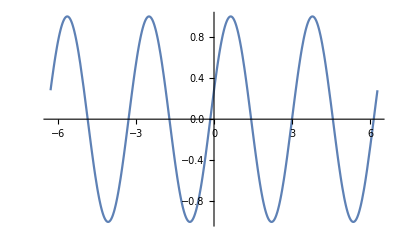

```mathematica
funkcija = Sin[(2x + Pi/4) - 1/2]
Plot[funkcija, {x, -2Pi, 2Pi}]
```

## 7. Naloga

```mathematica
ClearAll[funkcija]
```

```mathematica
funkcija1 = 5Sin[x-2];
funkcija2 = 2^x - 6;
```

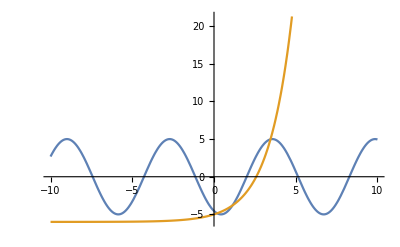

```mathematica
Plot[{funkcija1,funkcija2} , {x, -10, 10}]
```

## 8. Naloga

```mathematica
ClearAll[a, b]
a = 3^200 + 20;
b = 2^300 + 30;
a > b
```

True

```mathematica
b > a
```

False

```mathematica
a == b
```

False

## 9. Naloga

```mathematica
Solve[x^2 + 4x + 2 == 0]
```

{{x→-2-√2},{x→-2+√2}}

```mathematica
Solve[x^2 + 4x + 5 == 0]
```

{{x→-2-ⅈ},{x→-2+ⅈ}}

## 10. Naloga

```mathematica
ClearAll[x]
```

```mathematica
Reduce[x^4 == 1]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

## 11. Naloga

```mathematica
ClearAll[funkcija]
```

```mathematica
funkcija = (x^2 - CubeRoot[x^2]) E^x
```

ⅇ^x (x^2-(x^2)^(1/3))

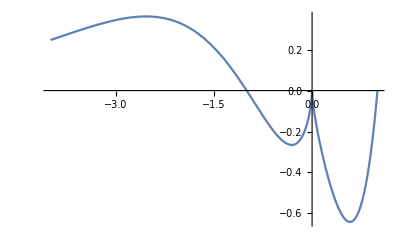

```mathematica
Plot[funkcija, {x,-4, 1}]
```

```mathematica
Solve[funkcija == 0]
```

{{x→-1},{x→0},{x→1}}

```mathematica
Reduce[funkcija == 0]
```

x==-1||x==0||x==1

INFO:
f[x_] := Sin[x] (definiranje funkcije)

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

- = je desna stran gre v levo
- == je pa dejanski =